### Match heights

Spacetime versions aren’t particularly revealing in these cases:

Match heights

```mathematica
GraphicsRow[Framed[#,FrameStyle->Gray]&/@(GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{$LifeData[#]["MatrixData"],0},24,ViewPoint->{0.9079906233946544,-2.941346308654788,1.4050035303835495}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData[#]["MatrixData"],0},24]},ImageSize->{Automatic,150}]&/@{"Carnival shuttle","Mold on fire-spitting"})]
```

-Graphics-

```mathematica
GraphicsRow[Framed[#,FrameStyle->Gray]&/@(GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{$LifeData[#]["MatrixData"],0},24,ViewPoint->{0.9079906233946544,-2.941346308654788,1.4050035303835495}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData[#]["MatrixData"],0},24, ImageSize->{Automatic, If[# ==="Carnival shuttle",  340, 140]}]},ImageSize->{Automatic,140}]&/@{"Carnival shuttle","Mold on fire-spitting"}), Spacings->30]
```

-Graphics-

### Combine these on one line. Box things etc.

But the causal graphs give a much better picture:

Combine these on one line.  Box things etc.

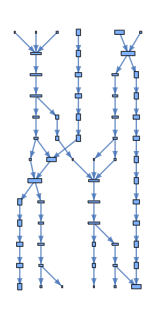
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
Row[Framed[#,FrameStyle->Opacity[.3]]&/@{PatternsLayeredGraph[$LifeData["Carnival shuttle"],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&)],BoundingBoxLayeredGraph[$LifeData["Carnival shuttle"]]},Spacer[20]]
```

```mathematica
Row[Framed[#,FrameStyle->Opacity[.3]]&/@{PatternsLayeredGraph[$LifeData[#],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&)],BoundingBoxLayeredGraph[$LifeData[#]]},Spacer[20]]&["Mold on fire-spitting"]
```

-Graphics--Graphics-

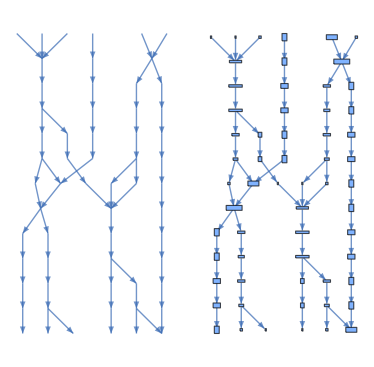
-Graphics--Graphics-

```mathematica
Row[
MapIndexed[Framed[GraphicsRow[#, Spacings->If[First[#2]==1, 10, {{2-> 10, 3->15}, 3}]], FrameStyle->Gray]&,Partition[Join[{PatternsLayeredGraph[$LifeData["Carnival shuttle"],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 350}],BoundingBoxLayeredGraph[$LifeData["Carnival shuttle"], Automatic, ImageSize->{Automatic, 350}]},
{PatternsLayeredGraph[$LifeData[#],Automatic,"VertexSizeFunction":>(10 Sqrt[Dimensions[#]]&), ImageSize->{Automatic, 365}, PlotRangePadding->{0, 0}],BoundingBoxLayeredGraph[$LifeData[#], Automatic, ImageSize->{Automatic, 340}, EdgeShapeFunction->"Arrow"]}&["Mold on fire-spitting"]
], 2]], Spacer[25]]
```

### Add pattern callout. Possibly add horizontal guides.

But after that, for nearly two decades, no more spaceships were found.  In 1989, however, a systematic method for searching was invented, and in the years since, a steady stream of new spaceships have been found.  A variety of different periods have been seen

Add pattern callout
Possibly add horizontal guides

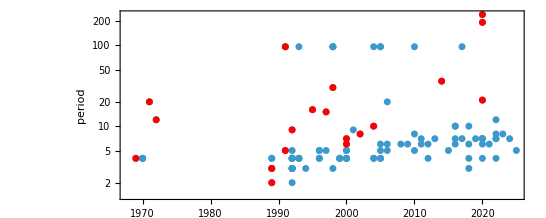

```mathematica
With[{data=Values[{#Year,#Period}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log"]]
```

Not right, bit of a challenge with the log scaling

Fix padding, fix non-red starters,

```mathematica
ListPlot[MapIndexed[Callout[Style[ {#Year, #Period},If[Last[#2] == 1 || #Name ==="13-engine Cordership",Red, None]], If[Times@@Dimensions[#MatrixData]>2000, None, CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10, ImageSize->{30, 30}, Mesh->False, FrameStyle->Opacity[.3]]]]&,(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&]), {2}], Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log",PlotStyle-> Directive[RGBColor[0.24, 0.6, 0.8], PointSize[.011]],
Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,Log[#Period]},{-1,0}]&/@(SortBy[#, #Year&]&/@GatherBy[Values@Select[$LifeData,#Class==="Spaceship"&], #Period&])[[All, -1]]}),
PlotRangePadding->{{1, 1}, {Automatic, .25}}
]
```

-Graphics-

### Make

Adding just one still-life block to the so-called “switch engine”

Make

PM: make first pic smaller?

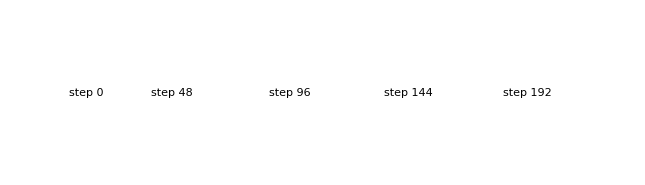

```mathematica
GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},#],Text[Style[StringTemplate["step ``"][#],Gray,9]]]&/@{0,48,96,144,48 4}]
```

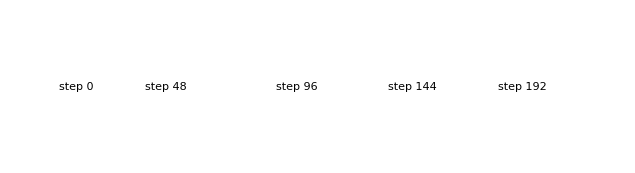

```mathematica
GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},#, ImageSize-> If[# == 0, {Automatic, 100}, {Automatic, 150}]],Text[Style[StringTemplate["step ``"][#],Gray,9]]]&/@{0,48,96,144,48 4}]
```

### Drop a line from the frame tick to wherever the structure was first discovered

Here’s a more detailed picture, showing the relative amount of use of each part in structures from each year:

Drop a line from the frame tick to to the year the structure was first discovered

Get rid of the 0 on the rank scale ... as well as the space at the beginning

```mathematica
resall = ;
```

```mathematica
activity = Module[{rrr, xr},
rrr=Association[DeleteCases[Union[#],None]&/@Association[resall]];
xr=Flatten[KeyValueMap[Thread[#2->$LifeData[#1]["Year"]]&,Association[rrr]]];
#->Cases[xr,(#->x_)->x]&/@Keys[Take[ReverseSort[Counts[Flatten[Values[rrr]]]],32]]];
```

```mathematica
fcef[{{xmin_,xmax_},{ymin_,ymax_}},v_,meta_,style___]:={Rectangle[{xmin,ymin},{xmax,ymax}]}
```

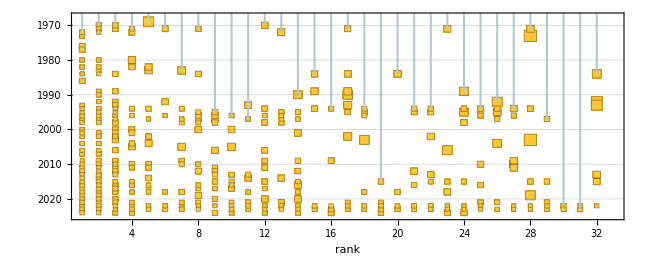

```mathematica
With[{totsyear=KeySort[Merge[Values[Counts/@Take[Association[activity],32]],Total]],totsitem=Total/@Values[Counts/@Take[Association[activity],32]]},BubbleChart[Catenate[MapIndexed[Function[{assoc,idx},KeyValueMap[{First@idx,#1,(#2/totsyear[#1])/totsitem[[First@idx]]}&,assoc]],Values[Counts/@Take[Association[activity],32]]]],ChartElementFunction->fcef,ScalingFunctions->{Automatic,"Reverse"},PlotRange->{{1,33},Automatic},PlotRangePadding->{{Automatic,None},{Automatic,Automatic}},AspectRatio->.4,GridLines->{None,Range[1970,2020,10]},BubbleScale->"Area",BubbleSizes->{.02,.06},FrameTicks->{{Automatic,Automatic},Reverse[{Transpose[{Range[1,32,1],CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#]["MatrixData"],0},0,ImageSize->{20,20},Mesh->None,MeshStyle->Opacity[.05]]&/@Keys[Take[Association[activity],32]]}],Automatic}]},ImageSize->650,FrameLabel->{"rank",None},
Epilog->{Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],MapIndexed[Line[{ {First@#2, 0},{First@#2,-#1}}]&, activity[[All, 2, 1]]],
Red,PointSize[.1], Point[{10, 10}]
}, PerformanceGoal->"Speed"
]]
```

### Vertical dividers only

```mathematica
ld = {{"[◼]", "Data"}}["$LifeData"];
allimps = Table[Module[{p3=SortBy[Select[ld,#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

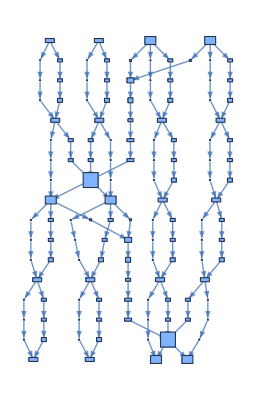
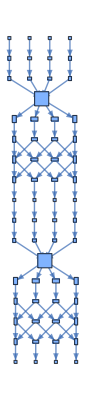
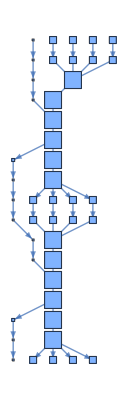
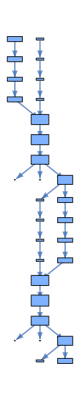
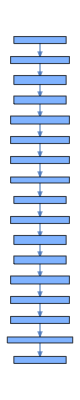
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-
1983 | 1994 | 1994 | 2016 | 2020

```mathematica
Grid[{
Column[{
{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic(*, ImageSize->{125, 210} *)(*PlotRange-> {{-15, 8}, Automatic}*)],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},16, ImageSize->{90, 75}
(*6 Sqrt[Last[Dimensions[#MatrixData]]]*)(*{75, 50}*)]}, Spacings->{0,1.5},Alignment->Center] &/@SortBy[allimps[[15]],#Year&],
Style[Text[#Year], 11,GrayLevel[0.25]]&/@SortBy[allimps[[15]],#Year&]
},(*Frame->{None, Automatic},*)FrameStyle->Opacity[.2],Dividers->{All,False}, Alignment->Center, Spacings->{1, {1.5,.2}}]
```

### Clean up

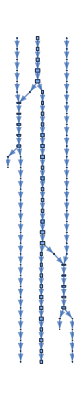
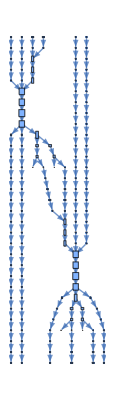
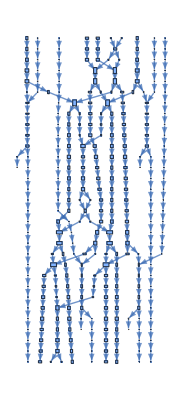
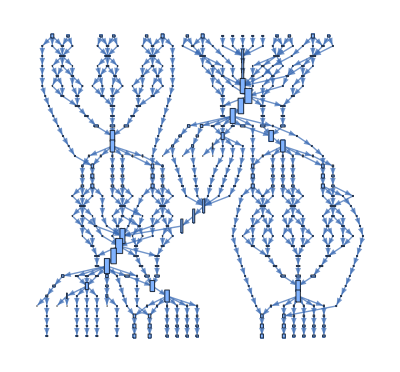
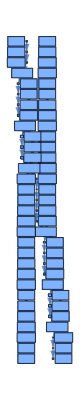
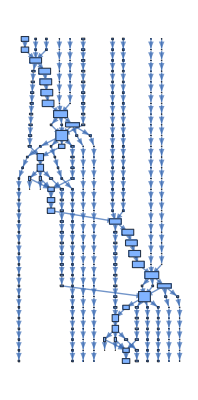
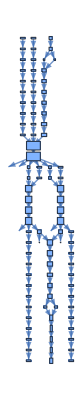
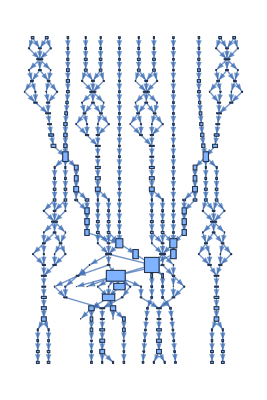
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics-1970
3.2 | -Graphics-1980
5.1 | -Graphics-1984
9.6 | -Graphics-1985
16. | -Graphics-1995
2.8 | -Graphics-2022
9.5 | -Graphics-2022
3.1 | -Graphics-2022
11. | -Graphics-2023
3.7

```mathematica
Grid[Transpose[Values[{GraphPlot[BoundingBoxLayeredGraph[#,Automatic], ImageSize->{Automatic, 145}],
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->10 Sqrt[Last[Dimensions[#MatrixData]]], MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.4)]],Column[Text/@{#Year,N[VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period,2]}]]}&/@SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==30&]//Quiet,#Year&]]],(*Spacer[2],*)Dividers->{All, False},FrameStyle->Opacity[.2], Alignment->Top]
```

```mathematica
Grid[Transpose[Values[{GraphPlot[BoundingBoxLayeredGraph[#,Automatic], ImageSize->{Automatic, 145}],
Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->(*10 Sqrt[Last[Dimensions[#MatrixData]]],*)If[#Name ==="p30rpentominohassler2" , {Automatic, UpTo[75]}, {UpTo[75], Automatic}],MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.4)]], If[#Name ==="p30rpentominohassler2", 0, Pi/2]] ,Column[Style[Text[#], 11]&/@{#Year,Round[N[VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period,3], .1]}]}&/@SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==30&]//Quiet,#Year&]]],(*Spacer[2],*)Dividers->{All, False},FrameStyle->Opacity[.2], Alignment->Center]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1970
3.2 | 1980
5.1 | 1984
9.6 | 1985
16.3 | 1995
2.8 | 2022
9.5 | 2022
3.1 | 2022
11.1 | 2023
3.7

### Dotted lines

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[getvector[#]],0] &,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}];
```

```mathematica
redidxs =With[{ps = PositionSmallest[#, 1][[1, -1]]&/@Map[#Year&, GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&],{2}]},
Association@Table[i->ps[[i]], {i, Length[ps]}]];
```

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Callout[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, None,CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, 10(*Min[5#Period, 100]*),Mesh->False, MeshStyle->Opacity[.05], ImageSize->{100, 100}]], LabelStyle->20]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,If[MatchQ[#,_Rational],InputForm[#], Row[{"√5","/",6}] ]}&/@DeleteCases[Union[Last/@data],1/8|1/7],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],
PlotMarkers->Catenate[MapIndexed[{Rotate[Graphics[{{AbsolutePointSize[5],Style[Point[{0, 0}], If[Last[#2] == redidxs[First[#2]], Red, None]]},Style[Text[Style["⟶",Bold, GrayLevel[.2],7],Scaled[{.75,.525}]],GrayLevel[.3]]}],#], 30}&, as, {2}]], PlotRangePadding->{{Automatic, .1}, {Automatic, 0}}, GridLines->{None, Automatic}, GridLinesStyle->Directive[Opacity[.6],Gray, Dotted]]]
```

-Graphics-

### Using ”PerformanceGoal->Speed” to lower memory size of bubble charts

Old vs. new bytecount

```mathematica
ByteCount/@ {, }
```

{996072,602688}

Old

```mathematica
(*partcounts=ParallelMap[{#Name,#["Year"],If[#MatrixData["ExplicitLength"]<10^5,Length[CausalSeparation[#["MatrixData"]["ExplicitPositions"]]],TooBig]}&,$LifeData];*)
```

```mathematica
(*Iconize[partcounts]*)
```

```mathematica
partcounts=;
```

```mathematica
partsbydate=Values[Last/@#]&/@GroupBy[partcounts,#[[2]]&];
```

```mathematica
BubbleChart[KeyValueMap[Append,Counts[Catenate[KeyValueMap[{x,y}|->{x,#}&/@y,partsbydate]]]],Frame->True,AspectRatio->.4,ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"number of modular parts"},ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]],PlotRangePadding->{{-.5, -.5}, Automatic}]
```

-Graphics-

New

```mathematica
partcounts=;
```

```mathematica
partsbydate=Values[Last/@#]&/@GroupBy[partcounts,#[[2]]&];
```

```mathematica
BubbleChart[KeyValueMap[Append,Counts[Catenate[KeyValueMap[{x,y}|->{x,#}&/@y,partsbydate]]]],Frame->True,AspectRatio->.4,ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"number of modular parts"},ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]],PlotRangePadding->{{-.5, -.5}, Automatic}]
```

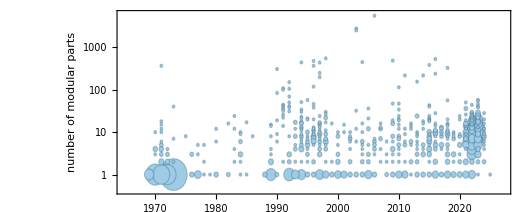

```mathematica
BubbleChart[KeyValueMap[Append,Counts[Catenate[KeyValueMap[{x,y}|->{x,#}&/@y,partsbydate]]]],Frame->True,AspectRatio->.4,ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"number of modular parts"},ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]],PlotRangePadding->{{-.5, -.5}, Automatic}, PerformanceGoal->"Speed"]
```

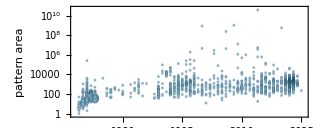
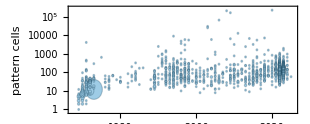

```mathematica
Row[{BubbleChart[KeyValueMap[Append,Counts[Values[{#Year,Times@@Dimensions[#MatrixData]}&/@$LifeData]]],Frame->True,AspectRatio->.4,ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"pattern area"},ImageSize->310,
ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]], PerformanceGoal->"Speed"],BubbleChart[KeyValueMap[Append,Counts[Values[{#Year,Length[#MatrixData["ExplicitValues"]]}&/@$LifeData]]],Frame->True,AspectRatio->.4,ScalingFunctions->{Automatic,"Log",Automatic},FrameLabel->{None,"pattern cells"},ImageSize->310,
ChartStyle->Directive[Lighter[ColorData["DefaultPlotColors"][1],.5],EdgeForm[Darker[ColorData["DefaultPlotColors"][1],.5]]], PerformanceGoal->"Speed"]},Spacer[20]]
```